## Manipulate Part 2

Hello and welcome to the second part of our lectures on Manipulate.

### Introduction

Today we are going to learn how to build this:

```mathematica
Manipulate[
GraphicsGrid[{
{
Graphics[{
Circle[{0,0},1],
Disk[{0,0},0.05],
Circle[{Cos[t],Sin[t]},0.05],
Line[{{0,0},{Cos[t],Sin[t]}}]
},PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1],
Plot[Sin[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}},AspectRatio->1]
},{
Rotate[Plot[Cos[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}},AspectRatio->1],-Pi/2]
}
}],
{t,0.001,8Pi}]
```

So what is this? In a previous lecture we used ParametricPlot to plot a circle where x=cos(t), y=sin(t), and t was our independent parameter, which in this case is the angle from the positive x-axis. In this animation we can actually visualize the x and y coordinates of the circle over time. So let’s begin!

### Drawing the Model

The first thing we need to do is make the circle:



```mathematica
Graphics[{
Circle[{0,0},1]
}]
```

Now let’s add our tracing circle, and we’ll place it at t=1 (for now):

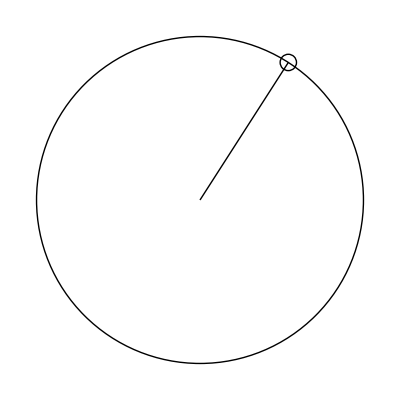

```mathematica
Graphics[{
Circle[{0,0},1],
Circle[{Cos[1],Sin[1]},0.05],
Line[{{0,0},{Cos[1],Sin[1]}}]
}]
```

Now let’s add the disk at the center:

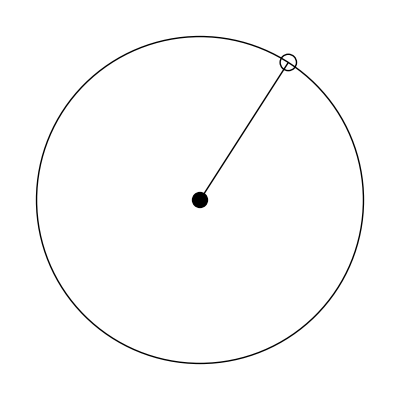

```mathematica
Graphics[{
Circle[{0,0},1],
Disk[{0,0},0.05],
Circle[{Cos[1],Sin[1]},0.05],
Line[{{0,0},{Cos[1],Sin[1]}}]
}]
```

### Animating the Model

Now, let’s wrap this up in a Manipulate and replace our instances of 1 with the variable t:

```mathematica
Manipulate[
Graphics[{
Circle[{0,0},1],
Disk[{0,0},0.05],
Circle[{Cos[t],Sin[t]},0.05],
Line[{{0,0},{Cos[t],Sin[t]}}]
}],
{t,0,8Pi}]
```

Now we should be able to drag our slider. It looks pretty good aside from the fact that it bounces a little. The reason for the bouncing is that as we drag the slider, Mathematica notices that it needs more space over here, so it shrinks the image on the x-axis here, and you reach the bottom, it shrinks it vertically. So what we need to do is tell Mathematica the range over which we want to plot values. So we can add that to the Graphics object. We use PlotRange.

```mathematica
Manipulate[
Graphics[{
Circle[{0,0},1],
Disk[{0,0},0.05],
Circle[{Cos[t],Sin[t]},0.05],
Line[{{0,0},{Cos[t],Sin[t]}}]
},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],
{t,0,8Pi}]
```

So you see it shrunk a little. And now when we drag our slider, no more bouncing. Beautiful!

### Multiple Graphics with GraphicsGrid

So now we need to take this circle and put it next to a Sine plot and put it above a Cosine plot. In order to do that, we are going to need a new function GraphicsGrid. In previous lectures we saw GraphicsRow, which allowed us to put multiple graphics one after the next. Now we need to be able to put a graphic in the top left, and the right and below. So we are going to use GraphicsGrid for that.

```mathematica
?GraphicsGrid
```

GraphicsGrid[{{g_11,g_12,…},…}] generates a graphic in which the g_ij are laid out in a two-dimensional grid.

So GraphicsGrid takes a list of lists.  The top level list basically takes a list of rows, and each embedded list is the set of columns. So let’s start by creating our first row. So we say

```mathematica
Manipulate[
GraphicsGrid[{
{
Graphics[{
Circle[{0,0},1],
Disk[{0,0},0.05],
Circle[{Cos[t],Sin[t]},0.05],
Line[{{0,0},{Cos[t],Sin[t]}}]
},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],
Plot[Sin[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}}]
}
}],
{t,0.001,8Pi}]
```

Let’s add the next row.

```mathematica
Manipulate[
GraphicsGrid[{
{
Graphics[{
Circle[{0,0},1],
Disk[{0,0},0.05],
Circle[{Cos[t],Sin[t]},0.05],
Line[{{0,0},{Cos[t],Sin[t]}}]
},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],
Plot[Sin[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}}]
},{
Plot[Cos[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}}]
}
}],
{t,0.001,8Pi}]
```

Now we have our Sine and Cosine. We are going to need the Rotate function.

```mathematica
?Rotate
```

Rotate[g,θ] represents 2D graphics primitives or any other objects g rotated counterclockwise by θ radians about the center of their bounding box. 
Rotate[g,θ,{x,y}] rotates about the point {x,y}. 
Rotate[g,{u,v}] rotates around the origin, transforming the 2D or 3D vector u to v.
Rotate[g,θ,w] rotates 3D graphics primitives by θ radians around the 3D vector w anchored at the origin.
Rotate[g,θ,w,p] rotates around the 3D vector w anchored at p.
Rotate[g,θ,{u,v}] rotates by angle θ in the plane spanned by 3D vectors u and v.

Rotate takes a graphics object and rotates it by θ in radians.We are going to need to rotate it by -π/2.

```mathematica
Manipulate[
GraphicsGrid[{
{
Graphics[{
Circle[{0,0},1],
Disk[{0,0},0.05],
Circle[{Cos[t],Sin[t]},0.05],
Line[{{0,0},{Cos[t],Sin[t]}}]
},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],
Plot[Sin[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}}]
},{
Rotate[Plot[Cos[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}}],-Pi/2]
}
}],
{t,0.001,8Pi}]
```

Nice! Now one of the things that GraphicsGrid does is assumes the cells have the same size, which is why these numbers are getting clipped here. One way we can make everything look better is by making everything the same size. In order to do that, we need to start by telling Mathematica what the sizes of these things should be. A really easy way to do that is to say that the AspectRatio is one. That way we get back only square figures. So let’s do that to each of our objects.

```mathematica
Manipulate[
GraphicsGrid[{
{
Graphics[{
Circle[{0,0},1],
Disk[{0,0},0.05],
Circle[{Cos[t],Sin[t]},0.05],
Line[{{0,0},{Cos[t],Sin[t]}}]
},PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1],
Plot[Sin[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}},AspectRatio->1]
},{
Rotate[Plot[Cos[x],{x,0,t},PlotRange->{{0,8Pi},{-1.1,1.1}},AspectRatio->1],-Pi/2]
}
}],
{t,0.001,8Pi}]
```

So now we have only square cells, and everything looks tidy!

### Summary

This concludes our lecture on Manipulate. Manipulate is a pretty powerful function and I’m sure we are going to use it again in future lectures. I hope you had fun and I’ll see you at the next lecture!